```mathematica
vpairs = {{3700, 1750}, {4200, 1500}, {3680, 1500}, {1200, 1000}, {800, 1000}, {1000, 750}, {120, 500}, {90, 250}, {100, 750}}
```

{{3700,1750},{4200,1500},{3680,1500},{1200,1000},{800,1000},{1000,750},{120,500},{90,250},{100,750}}

```mathematica
cm =  ClusterClassify[vpairs]
```

ClassifierFunction[…]

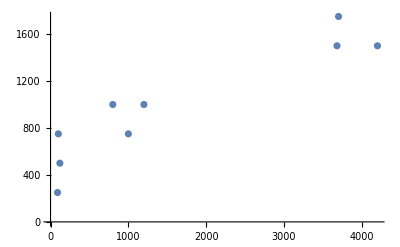

```mathematica
ListPlot[vpairs]
```

```mathematica
GatherBy[vpairs, cm]
```

{{{3700,1750},{4200,1500},{3680,1500}},{{1200,1000},{800,1000},{1000,750},{120,500},{90,250},{100,750}}}